```mathematica
;
```

```mathematica
Needs["RootSearch`"]

fullSimplifyReal[x_]:=Assuming[_Symbol ∈ Reals , FullSimplify@x]
myFormatConvertToNegativePowers = StandardForm[#/.Power[expr_, r_?Negative] :> Superscript[expr,r] ]&;

CL=2.997925 10^10;
Gr=6.67 10^-8;
ARAD=7.56464 10^(-15);

KPE=0.4;
KPDUST = 50;       (* dust kappa *)

SGT=6.6524 10^-25; (*Thomson cross section cm^2*)
RGAS=8.31 10^7/μm/.μm->1.;
KB=1.38062 10^-16;
PC=3.085678 10^18;
Msol=1.989 10^33;

MBH=10^7 Msol;

MP=1.672661 10^-24;
SGB = ARAD*CL/4;
DAY = 24 3600;
YR=31536000;
MsolYr = Msol/YR;
KM=10^5;

rulzGlob = {α->0.1, ϵ->0.1, η->0.1,  M->MBH, μ->1};
			
rulForConst={J->1, m->1,Rg->RGAS, σ->SGB, a->ARAD, G->Gr,c->CL, a->ARAD};

CalculateMdotNumber[rul_, excess_] := Module[{res},
	res =excess* μ η ϵ^-1 4Pi CL Gr M /KPE/CL^2/.rul];
```

Needs::nocont: Context RootSearch` was not created when Needs was evaluated.

```mathematica
RandomInteger[{1,10^9}]
```

219020674

FindRoot::nlnum: The function value {eq[1.]} is not a list of numbers with dimensions {1} at {T} = {1.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

General::munfl: Exp[-76799.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-31755.7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-22206.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

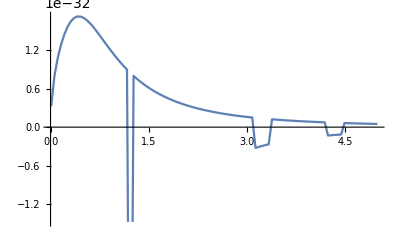

```mathematica
(*                   single layer disk                             *)
ClearAll[NSolve2LayerDisk, NSolveDisk,X,X1,EqTcSingleLayer,κ,r,T,
			NSolveDisk,NDiskTc];
ClearAll[Tc,Tsf,TcMat,TsfMat,X1,MdotRange,lenTc,rTc,Nmdot,MdotMin,MdotMax];

NSolveDisk[R_, NMdot_:0.2MsolYr, OmegaSlope_:1.5, R0_:0.01PC ] := Module[ {EqTc,NSolvTc,FindSolForT, EqTcSingleLayer,
Omega,HeightGasAndRad,MinTAtRadius,NKappa,NTsurf, Tc,Fz, X1,KPD,Tsub,res,Tc1, NTc1,TcRange,HeightRange,minTAtRad,ΣColDens,ΣRange,ρRange,Pgas,Prad},
	
KPD=KPDUST;
Tsub=1500;
  
Tsf[r_]:=((3/π)^(1/4) ((G J M Mdt)/(r^3 σ))^(1/4))/2^(3/4)/.rulForConst/.rulzGlob;

Omega[r_] := Module[{Ω0 = G^(1/2) MBH^(1/2) R0^(-3/2)},
					 Ω0(R0/r)^OmegaSlope];
NKappa[t_]:= Block[ {Ts = Tsub, ΔT=0.1, κ0=KPE, κ1=KPD},
			KPE + κ1(1+ Exp[-(t-Ts )/ΔT])^-1;
			KPD
			];
			
MinTAtRadius[r_]:=Module[{eqH,minT},
				minT=((3/2)^(1/5) J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5) Ω^(3/5))/(2 π^(2/5) Rg^(1/5) α^(1/5) σ^(1/5))/.κ->KPE/.Ω->Omega[r]/.b->ARAD/.rulForConst/.rulzGlob/.Mdt->NMdot;
				eqH[T_]:=(-(32 π Rg T σ)/(3 J m Mdt κ b  Ω^2)+(J Mdt Ω)/(2 π T^4 α b))/.κ->NKappa[T]/.Ω->Omega[r]/.b->ARAD/.rulForConst/.rulzGlob/.Mdt->NMdot;

				FindRoot[eq[T]==0,{T,1,minT}] ];

ΣColDens[r_,T_]:=(64 π T^4 σ)/(9 J Mdt κ Ω^2)/.κ->NKappa[T]/.Ω->Omega[r]/.b->ARAD/.rulForConst/.rulzGlob/.Mdt->NMdot;
Fz= 3/8 Mdt  Ω^2;

EqTcSingleLayer[T_,r_]:= (-27 a^2 G^(5/2) J^4 m^2 M^(5/2) Mdt^4 r^(3/2) T^4 α κ^3+
               16 σ (3 G^(3/2) J^2 m M^(3/2) Mdt^2 κ - 64 π^2 r^(9/2) Rg T^5 α σ)^2)/.κ->NKappa[T]/.rulForConst/.rulzGlob/.Mdt->NMdot;


HeightGasAndRad[r_,T_] := Module[{Tcc},
		(-(32 π Rg T σ)/(3 J m Mdt κ b  Ω^2) + (J Mdt Ω)/(2 π T^4 α b))/.κ->NKappa[T]/.Ω->Omega[r]/.b->ARAD/.rulForConst/.rulzGlob/.Mdt->NMdot
		];


minTAtRad=(MinTAtRadius[#]&/@ R)⟦All,1,2⟧;

TcRange=(MapThread[Quiet[FindRoot[EqTcSingleLayer[T,#1],{T,1,#2}]]&,{R,minTAtRad}])⟦All,1,2⟧;

HeightRange=MapThread[HeightGasAndRad[#1,#2]&, {R,TcRange}];

ΣRange=MapThread[ΣColDens[#1,#2]&,  {R,TcRange}];

ρRange = ΣRange/(2 HeightRange);

{ρRange,TcRange,HeightRange,ΣRange}
];


xmin=0.01; xmax=5; Nx1=100;
X1 =  Range[xmin,xmax,(xmax-xmin)/(Nx1-1)];
X1 =  X1;


{ρc, Tc, hc, Σc}= NSolveDisk[ PC X1, 5MsolYr, 1.5];

pltT=ListPlot[MapThread[{#1,#2/(PC #1)}&, {X1, ρc}], Joined->True]
```

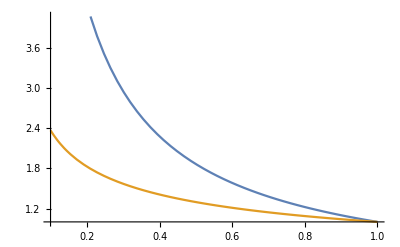

```mathematica
Plot[{x^(-9/10),x^(-3/8)},{x, 0.1, 1}]
```

## Naive estimates of the disk thickness :

```mathematica
MdotCr= Solve[3/(8Pi) Mdot/(c R)κ == H2R, Mdot]⟦1⟧⟦1⟧⟦2⟧

H2R=0.1;

R=0.1PC;

(MdotCr/.rulForConst/.κ->KPDUST)/MsolYr

HeightGasAndRad[r_,T_] :=3/(8Pi) Mdot/CL κ;

ClearAll[MdotCr,H2R,R,Mdot,HeightGasAndRad]
```

(8 c H2R π R)/(3 κ)

2.45749

{{0.140559,0.412471,0.543815,0.640962,0.720444,0.788728,0.849127,0.9036,0.953417,0.999457},{0.00802195,0.011143,0.011989,0.0125247,0.0129303,0.0132646,0.0135549,0.013816,0.0208433,0.0204617}}

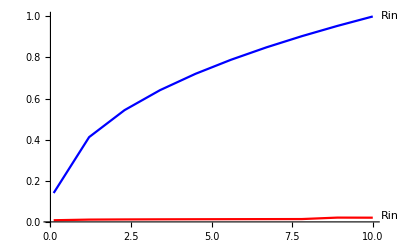

```mathematica
(Ro-Ri)/Ro=1 - Ri/Ro
```

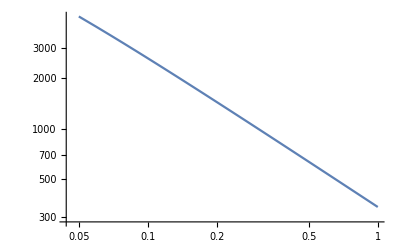

```mathematica
(* dust sublimation range *)
ClearAll[Tc,Tsf,TcMat,TsfMat,X1,MdotRange,lenTc,rTc,Nmdot,MdotMin,MdotMax]

xmin=0.05; xmax=1; Nx1=100;
X1 =  Range[xmin,xmax,(xmax-xmin)/(Nx1-1)];

{Tc, Tsf} = Quiet@ NDiskTc[ PC X1, 0.2MsolYr, 1.5];

pltT=ListLogLogPlot[MapThread[{#1,#2}&, {X1, Tc}], Joined->True]
```

Calculate varios properties of the disk a a function of mass-loss rate Ṁ

rTc = {6780.67→0.0937671}

rTc = {6780.67→0.12154}

rTc = {6780.67→0.151816}

rTc = {6780.67→0.172222}

rTc = {6780.67→0.192395}

rTc = {6780.67→0.212436}

rTc = {6780.67→0.222851}

rTc = {6780.67→0.242725}

rTc = {6780.67→0.252997}

rTc = {6780.67→0.263223}

rTc = {6780.67→0.282978}

rTc = {6780.67→0.293129}

rTc = {6780.67→0.303252}

rTc = {6780.67→0.313351}

rTc = {6780.67→0.32343}

rTc = {6780.67→0.333491}

rTc = {6780.67→0.343536}

rTc = {6780.67→0.353568}

rTc = {6780.67→0.35398}

rTc = {6780.67→0.363979}

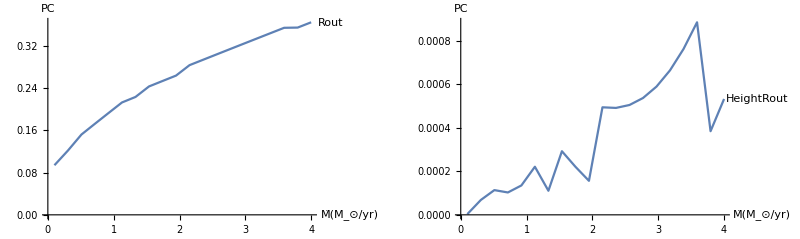

```mathematica
Print[" Calculate varios properties of the disk a a function of mass-loss rate Ṁ "];

(* dust sublimation range *)


ClearAll[Tc,Tsf,TcMat,TsfMat,X1,MdotRange,lenTc,rTc,rTsf,Nmdot,MdotMin,MdotMax,pltIn,pltOut,pltHeightOut,hRc1,HeightRad];


xmin=0.001; xmax=1; Nx1=100;

X1 =  Range[xmin,xmax,(xmax-xmin)/(Nx1-1)];

Nmdot = 20;
MdotMin = 0.1;
MdotMax = 4;
MdotRange = MsolYr Range[MdotMin, MdotMax, (MdotMax-MdotMin)/(Nmdot-1)];


HeightRad[Mdot_] := 3/(8 Pi) Mdot/CL KPDUST;


{rTc, rTsf, hRc1} = Module[{TcMat,TsfMat,Tc,Tsf,rTc1,rTsf1,rTsfVec,rTcVec,RadInFun,HeightAtRsub,HeightVec},
	rTcVec ={};
	rTsfVec ={};
	
	HeightVec={};
	RadInFun[Mdt_, Tsub_] := (G^(1/3) J^(1/3) MBH^(1/3) Mdt^(1/3) (3/π)^(1/3))/(2 Tsub^(4/3) σ^(1/3))/.rulForConst;
	
	For[i=1,i<=Length[MdotRange],i++,
			
			{Tc, Tsf, HeightAtRsub} = Quiet@ NDiskTc[ PC X1, MdotRange⟦i⟧, 1.5];
			
			TcMat = Quiet@ ListInterpolation[Tc, X1];
			TsfMat = Quiet@ ListInterpolation[Tsf, X1];
			
			HeightAtRsub = Quiet@ ListInterpolation[HeightAtRsub, X1];
			
			rTc1 = Quiet@ FindRoot[TcMat[x]==1500, {x,0.1,1}];
			(*rTsf = Quiet@ FindRoot[TsfMat[x]==1500, {x,0.1,1}];*)		
			rTsf1 = RadInFun[MdotRange⟦i⟧, 1500];
			
			(*Print["rTsf = ", rTsf, "\n"]*)
			Print["rTc = ", rTc1 ];			
			
			(*Print["Hrc = ", HeightAtRsub[rTc1⟦1,2⟧] ];*)			
			AppendTo[rTcVec,rTc1⟦1,2⟧];
			AppendTo[rTsfVec,rTsf1];
			AppendTo[HeightVec,HeightAtRsub[rTc1⟦1,2⟧]];
	];
	
{rTcVec, rTsfVec/PC, HeightVec/PC}
];

ClearAll[pltIn,pltOut,pltRat];

pltIn = MapThread[{#1,#2}&, {MdotRange/MsolYr, rTsf}];

pltOut = MapThread[{#1,#2}&, {MdotRange/MsolYr,rTc}];

pltRat = MapThread[{#1,#2}&, {MdotRange/MsolYr, rTc/rTsf}];

pltHeightOut = MapThread[{#1,#2}&, {MdotRange/MsolYr, hRc1}];

GraphicsGrid[{{
ListPlot[Labeled[pltOut, "Rout"], Joined->True, AxesLabel->{"Ṁ(M_⊙/yr)", "PC"}], 
ListPlot[Labeled[pltHeightOut, "HeightRout"], Joined->True, AxesLabel->{"Ṁ(M_⊙/yr)", "PC"}]}}
]

(*ListPlot[Labeled[pltIn,"Rin"], Joined->True, PlotStyle->{Red,Blue} ] *)
(*rTc=((Quiet@FindRoot[ListInterpolation[TcMat⟦#⟧,X1][x]==1500,{x,0.1,1}])  &/@    Range[lenTc])⟦All,1,2⟧*)
```

```mathematica
ClearAll[H2RatTc,HeightRad,Nmdot,MdotMin,MdotMax,MdotRange]
Nmdot = 20;
MdotMin = 0.1;
MdotMax = 4;
MdotRange = MsolYr Range[MdotMin, MdotMax, (MdotMax-MdotMin)/(Nmdot-1)];

RouTc[Mdt_,κ_,α_,Ts_] :=   (3^(2/9) (G M)^(1/3) Mdt^(4/9) κ^(2/9))/(2^(8/9) π^(4/9) (a c Rg Ts^5 α)^(2/9));

RouTc[Mdt,κ,α,Ts]
RouTc[0.2MsolYr Subscript[Mdt, 0.1],50 Subscript[κ, 50],0.1 Subscript[α, 0.1], 1500 Subscript[T, 1500]]/PC/.rulForConst/.{M->10^7 Msol Subscript[M, 7]}


H2RatTc[Mdt_,κ_,α_,Ts_] =(3^(7/9) Mdt^(5/9) (a c Rg Ts^5 α)^(2/9) κ^(7/9))/(4 2^(1/9) c (G M)^(1/3) π^(5/9))/.rulForConst;

H2RatTc[Mdt,κ,α,Ts];

H2RatTc[1MsolYr Subscript[Mdt, 1],50 Subscript[κ, 50],0.1 Subscript[α, 0.1], 1500 Subscript[T, 1500]]/.{M->10^7 Msol Subscript[M, 7]};

(*KPDUST
HeightRad[3 MsolYr]/(0.12PC)
*)

MapThread[{#1, #2}&, {MdotRange,rTc}];

(*MapThread[(HeightRad[#1]/(PC #2))&, {MdotRange,rTc}]*)

ClearAll[HeightRad]
```

(3^(2/9) (G M)^(1/3) Mdt^(4/9) κ^(2/9))/(2^(8/9) π^(4/9) (a c Rg Ts^5 α)^(2/9))

(0.279081 M_7^(1/3) Mdt_0.1^(4/9) κ_50^(2/9))/((T_1500^5 α_0.1)^(2/9))

main

Set::shape: Lists {ρc,Tc,hc,Σc} and Null are not the same shape.

MapThread::mptd: Object Tc at position {2, 2} in MapThread[{#1,#2}&,{{0.01,0.0149495,0.019899,0.0248485,0.029798,0.0347475,0.039697,«37»,0.227778,0.232727,0.237677,0.242626,0.247576,0.252525,«50»},Tc}] has only 0 of required 1 dimensions.

ListLogLogPlot::lpn: MapThread[{#1,#2}&,{{0.01,0.0149495,0.019899,0.0248485,0.029798,0.0347475,0.039697,«37»,0.227778,0.232727,0.237677,0.242626,0.247576,0.252525,«50»},Tc}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogLogPlot::lpn will be suppressed during this calculation.

ListLogLogPlot[MapThread[{#1,#2}&,{{0.01,0.0149495,0.019899,0.0248485,0.029798,0.0347475,0.039697,0.0446465,0.049596,0.0545455,0.0594949,0.0644444,0.0693939,0.0743434,0.0792929,0.0842424,0.0891919,0.0941414,0.0990909,0.10404,0.10899,0.113939,0.118889,0.123838,0.128788,0.133737,0.138687,0.143636,0.148586,0.153535,0.158485,0.163434,0.168384,0.173333,0.178283,0.183232,0.188182,0.193131,0.198081,0.20303,0.20798,0.212929,0.217879,0.222828,0.227778,0.232727,0.237677,0.242626,0.247576,0.252525,0.257475,0.262424,0.267374,0.272323,0.277273,0.282222,0.287172,0.292121,0.297071,0.30202,0.30697,0.311919,0.316869,0.321818,0.326768,0.331717,0.336667,0.341616,0.346566,0.351515,0.356465,0.361414,0.366364,0.371313,0.376263,0.381212,0.386162,0.391111,0.396061,0.40101,0.40596,0.410909,0.415859,0.420808,0.425758,0.430707,0.435657,0.440606,0.445556,0.450505,0.455455,0.460404,0.465354,0.470303,0.475253,0.480202,0.485152,0.490101,0.495051,0.5},Tc}],Joined→True]

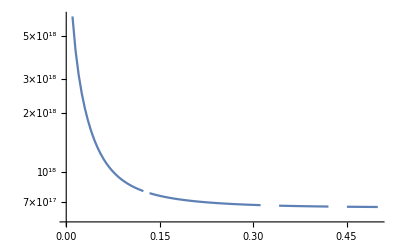

General::munfl: Exp[-115709.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-91705.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-75244.9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{7.87747×10^6,3.83268×10^6,2.57641×10^6,2.02725×10^6,1.73613×10^6,1.56231×10^6,1.45021×10^6,1.37412×10^6,1.32069×10^6,1.28239×10^6,1.25466×10^6,1.2346×10^6,1.22027×10^6,1.21033×10^6,1.20384×10^6,1.20008×10^6,1.19855×10^6,1.19885×10^6,406291.,423580.,440858.,458127.,475385.,492634.,509872.,527100.,544318.,561526.,578724.,595913.,613093.,630263.,647423.,664575.,681718.,698852.,715978.,733095.,750203.,767304.,784396.,801481.,818557.,835626.,852687.,869741.,886788.,903827.,920860.,937885.,954903.,971915.,988920.,1.00592×10^6,1.02291×10^6,1.0399×10^6,1.05688×10^6,1.07385×10^6,1.09081×10^6,1.10778×10^6,1.12473×10^6,1.14168×10^6,1.15862×10^6,1.17556×10^6,1.19249×10^6,1.20942×10^6,1.22634×10^6,1.24325×10^6,1.26016×10^6,1.27707×10^6,1.29397×10^6,1.31086×10^6,1.32775×10^6,1.34464×10^6,1.36151×10^6,1.37839×10^6,1.39526×10^6,1.41212×10^6,1.42898×10^6,1.44584×10^6,1.46269×10^6,1.47953×10^6,1.49637×10^6,1.51321×10^6,1.53004×10^6,1.54687×10^6,1.56369×10^6,1.58051×10^6,1.59733×10^6,1.61414×10^6,1.63094×10^6,1.64775×10^6,1.66454×10^6,1.68134×10^6,1.69813×10^6,1.71491×10^6,1.7317×10^6,1.74847×10^6,1.76525×10^6,1.78202×10^6}

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[MapThread[{#1,#2}&,{X1,ConvectiveFlux}],Joined→True]

main

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

General::munfl: Exp[-115709.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-91705.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-75244.9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

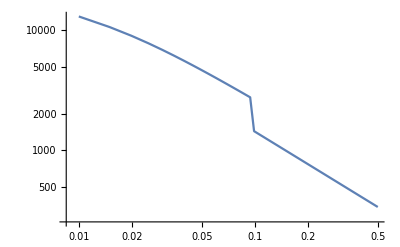

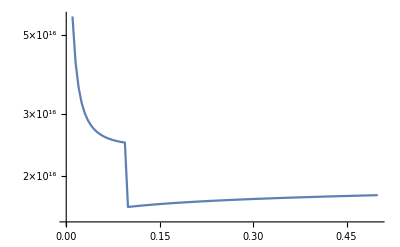

Set::shape: Lists {ConvectiveFlux,RadiationFlux} and ConvectiveFluxDisk[{5.52387×10^-12,7.38551×10^-12,7.89881×10^-12,7.65839×10^-12,7.10879×10^-12,6.47531×10^-12,5.85603×10^-12,«37»,1.86835×10^-12,1.80349×10^-12,1.74218×10^-12,1.68414×10^-12,1.62915×10^-12,1.57699×10^-12,«50»},«3»] are not the same shape.

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[MapThread[{#1,#2}&,{X1,ConvectiveFlux}],Joined→True]

```mathematica
(*                   double layer disk                             *)

NSolveDisk[R_] := Module[ {EqTc,NSolvTc,FindSolForT, EqTcSingleLayer,HeightGasAndRad,MinTAtRadius,NKappa,NTsurf, Tc,Fz, NMdot,X1,KPD,Tsub,res,Tc1, NTc1,TcRange,HeightRange,minTAtRad,ΣColDens,ΣRange,ρRange,Pgas,Prad},
	
KPD=KPDUST;
Tsub=1500;
NMdot=0.2MsolYr; 
 
Tsf[r_]:=((3/π)^(1/4) ((G J M Mdt)/(r^3 σ))^(1/4))/2^(3/4)/.rulForConst/.rulzGlob;

NKappa[t_]:= Block[ {Ts = Tsub, ΔT=0.1, κ0=KPE, κ1=KPD},
			KPE + κ1(1+ Exp[-(t-Ts )/ΔT])^-1
			];

(*Plot[ Sin[x], {t, 1000.,2000.} ];*)

   MinTAtRadius[r_]:=Module[{eq,minT},minT=((3/2)^(1/5) J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5) Ω^(3/5))/(2 π^(2/5) Rg^(1/5) α^(1/5) σ^(1/5))/.κ->KPE/.Ω->G^(1/2) MBH^(1/2) r^(-3/2)/.b->ARAD/.rulForConst/.rulzGlob/.Mdt->NMdot;

	eq[T_]:=(-(32 π Rg T σ)/(3 J m Mdt κ b  Ω^2)+(J Mdt Ω)/(2 π T^4 α b))/.κ->NKappa[T]/.Ω->G^(1/2) MBH^(1/2) r^(-3/2)/.b->ARAD/.rulForConst/.rulzGlob/.Mdt->NMdot;
]

]

(*--------------------------------------------------------------------*)
 "                         	main                         	"
(*--------------------------------------------------------------------*)

xmin=0.01;xmax=0.5; Nx1=100;
X1 =  Range[xmin,xmax,(xmax-xmin)/(Nx1-1)];
X1 =  X1;

{ρc, Tc, hc, Σc}= NSolveDisk[ PC X1];


pltT = ListLogLogPlot[MapThread[{#1,#2}&, {X1, Tc}], Joined->True]

pltH = ListLogPlot[MapThread[{#1,#2/#1}&, {X1, hc}], Joined->True]


(*
pltRoc=ListPlot[MapThread[{#1,#2}&, {X1, ρc}], Joined->True]
pltΣc=ListPlot[MapThread[{#1,#2}&, {X1, Σc}], Joined->True]*)
```

```mathematica
Solve[(-(32 π Rg T σ)/(3 J m Mdt κ b  Ω^2)+(J Mdt Ω)/(2 π T^4 α b))==0, T]//fullSimplifyReal
```

{{T→-((-3/2)^(1/5) J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5) Ω^(3/5))/(2 π^(2/5) Rg^(1/5) α^(1/5) σ^(1/5))},{T→((3/2)^(1/5) J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5) Ω^(3/5))/(2 π^(2/5) Rg^(1/5) α^(1/5) σ^(1/5))},{T→(J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5) Ω^(3/5) Root0.168+0.516 ⅈRoot[-3+64 #1^5&,5]0.16756010360999424)/(π^(2/5) Rg^(1/5) α^(1/5) σ^(1/5))},{T→(J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5) Ω^(3/5) Root0.168-0.516 ⅈRoot[-3+64 #1^5&,4]0.16756010360999424)/(π^(2/5) Rg^(1/5) α^(1/5) σ^(1/5))},{T→(J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5) Ω^(3/5) Root-0.439+0.319 ⅈRoot[-3+64 #1^5&,3]-0.43867804640941893)/(π^(2/5) Rg^(1/5) α^(1/5) σ^(1/5))}}

```mathematica
If[#<0,0,#]&/@ {1,2,3}
```

{1,2,3}

```mathematica
(-(32 π Rg T σ)/(3 J m Mdt κ b  Ω^2)+(J Mdt Ω)/(2 π T^4 α b))//Together//Numerator(*/.b->0*)
```

-64 π^2 Rg T^5 α σ+3 J^2 m Mdt^2 κ Ω^3

```mathematica
(-27 a b G^(5/2) J^4 m^2 M^(5/2) Mdt^4 r^(3/2) T^4 α κ^3+144 G J^2 m M Mdt^2 (G^2 J^2 m M^2 Mdt^2+4 (a-b) b π^2 r^6 Rg T^9 α^2) κ^2 σ-6144 G^(3/2) J^2 m M^(3/2) Mdt^2 π^2 r^(9/2) Rg T^5 α κ σ^2+65536 π^4 r^9 Rg^2 T^10 α^2 σ^3)/.b->0//FullSimplify
```

16 σ (3 G^(3/2) J^2 m M^(3/2) Mdt^2 κ-64 π^2 r^(9/2) Rg T^5 α σ)^2

-27 a b G^(5/2) J^4 m^2 M^(5/2) Mdt^4 r^(3/2) T^4 α κ^3+144 G J^2 m M Mdt^2 (G^2 J^2 m M^2 Mdt^2+4 (a-b) b π^2 r^6 Rg T^9 α^2) κ^2 σ-6144 G^(3/2) J^2 m M^(3/2) Mdt^2 π^2 r^(9/2) Rg T^5 α κ σ^2+65536 π^4 r^9 Rg^2 T^10 α^2 σ^3

```mathematica
PadeApproximant[Exp[-x],{x,0,{0,1}} ]
```

```mathematica
1/(1+x)
```

```mathematica
(1-x/2+x^2/12)/(1+x/2+x^2/12)
```

```mathematica
(1-x/2)/(1+x/2)
```

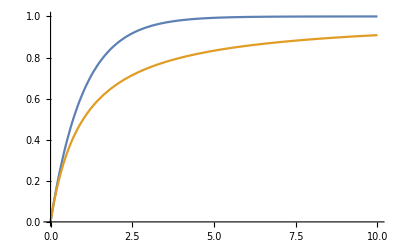

```mathematica
Plot[{(1-Exp[-x]),(1-1/(1+x))},{x,0,10}]
```

```mathematica
"Local flux "

 Solve[(3/8 Mdt  Ω^2 /.Ω->G^(1/2) M^(1/2) r^(-3/2))==1, r]
```

Local flux

{{r→-1/2 (-3)^(1/3) G^(1/3) M^(1/3) Mdt^(1/3)},{r→1/2 3^(1/3) G^(1/3) M^(1/3) Mdt^(1/3)},{r→1/2 (-1)^(2/3) 3^(1/3) G^(1/3) M^(1/3) Mdt^(1/3)}}

```mathematica
2.21 10^13/(2 Gr MBH/CL^2)
```

7.48589

## Local vs global radiation flux

```mathematica
Print@"(*     Local  radiation flux ergs:      *)"
```

```mathematica
ClearAll[FluxDisk,FluxAGN];
FluxDisk[r_, Mdot_,M_] := 3/(8Pi)(Gr M)/r^3 Mdot

FluxAGN[r_, ϵ_, Mdot_, θ_] := ϵ Mdot CL^2/r^2 Cos[θ](1+2Cos[θ]); 

FluxDisk[0.1PC , 0.1MsolYr, 10^7 Msol]

FluxAGN[0.1PC Subscript[r, 0.1], 0.1 Subscript[ϵ, 0.1],0.1MsolYr Subscript[M, 0.1], θ]//myFormatConvertToNegativePowers
```

33995.3

5.95345×10^9 Cos[θ] (1+2 Cos[θ]) M_0.1 ϵ_0.1 (r_0.1)^-2

33995.3

```mathematica
1500^4 SGB
```

2.87021×10^8

```mathematica
MsolYr CL^2/PC^2
```

5.95345×10^9

# Pgas = Prad

n=(a μ)/(3 m_p Rgas) T^3

```mathematica
(ARAD μ)/(3 Subscript[m, p] RGAS) T^3 /. {μ->1,Subscript[m, p]->MP,T->1500 Subscript[T, 1500]}
```

6.12254×10^10 T_1500^3